```mathematica
(*Attempting to solve Eq. (4) to get Fig. 3 of DOI: 10.1103/PhysRevB.88.144507.*)
Clear["Global`*"]
$PrePrint=#/.out_->TraditionalForm[out]&;
Dagger[m_]:=ConjugateTranspose[m]
MakeReal[xvar_]:={Im[xvar]^=0;Re[xvar]^=xvar;xvar*^=xvar;}
```

```mathematica
(*Useful mathematical definitions.*)
MakeReal[ϵ];MakeReal[ϕ];MakeReal[δ1];MakeReal[δ2];MakeReal[δp];MakeReal[δm];
ZeroMat[n_]:=ConstantArray[0,{n,n}];
σ[n_]:=PauliMatrix[n]
Σ1=ArrayFlatten[{{σ[1],0},{0,Id[2]}}];
σp={{0,1},{0,0}};
σm={{0,0},{1,0}};
Id[n_]:=IdentityMatrix[n]
antiCommutator[A_,B_]:=(A.B+B.A)
Commutator[A_,B_]:=(A.B-B.A)
SetSharedFunction[ParallelSow];
ParallelSow[expr_]:=Sow[expr]
```

```mathematica
(*The Majorana operators.*)
Maj[1]=KroneckerProduct[σ[1],σ[1]];
Maj[2]=KroneckerProduct[σ[1],σ[2]];
Maj[3]=KroneckerProduct[σ[1],σ[3]];
Maj[4]=KroneckerProduct[σ[2],Id[2]];

(*Bare fermions: these will be the quasiparticle operators.*)
Ann[1]=(1/2)(Maj[1]+ⅈ*Maj[2]);
Ann[2]=(1/2)(Maj[3]+ⅈ*Maj[4]);
Cre[1]=Dagger[Ann[1]];
Cre[2]=Dagger[Ann[2]];

(*BdG Hamiltonian*)
HBdG=({{2ϵ*Cos[ϕ/2],ⅈ*δm,0,ⅈ*δp},{-ⅈ*δm,0,-ⅈ*δp,0},{0,ⅈ*δp,-2ϵ*Cos[ϕ/2],ⅈ*δm},{-ⅈ*δp,0,-ⅈ*δm,0}})/2;
params2={ϵ->1,δp->1/10,δm->1/100};
ϵBdG1=Eigenvalues[HBdG][[2]]//.params2;
ϵBdG2=Eigenvalues[HBdG][[4]]//.params2;
```

```mathematica
(*This is the low-energy Hamiltonian in terms of Majoranas.*)
H0m=Simplify[(ⅈ*(ϵ)*Cos[ϕ/2]*Maj[1].Maj[2]+ⅈ*(1/2)(δp+δm)*Maj[1].Maj[3]+ⅈ*(1/2)(δp-δm)*Maj[4].Maj[2])/2]
evals=FullSimplify@Eigenvalues[H0m]
params1={ϵ->1,δp->1/10,δm->1/100};

(*Identifying energy eigenvalues in particle-hole pairs.*)
ϵ[1]=(evals[[4]]-evals[[2]]);
ϵ[2]=(evals[[4]]+evals[[2]]);
ϵ[-1]=-ϵ[1];
ϵ[-2]=-ϵ[2];

(*The low-energy Hamiltonian in terms of fermionic operators.*)
Hf0=((ϵ*Cos[ϕ/2]*(Cre[1].Ann[1]-(1/2)Id[4])+ⅈ*δp*Ann[1].Ann[2]+ⅈ*δm*Cre[1].Ann[2]))/2;
Hf=Hf0+Dagger[Hf0];
```

(-1/2 ϵ cos(ϕ/2) | -(ⅈ δp)/2 | 0 | 0
(ⅈ δp)/2 | 1/2 ϵ cos(ϕ/2) | 0 | 0
0 | 0 | -1/2 ϵ cos(ϕ/2) | -(ⅈ δm)/2
0 | 0 | (ⅈ δm)/2 | 1/2 ϵ cos(ϕ/2))

{-(√(2 δm^2+ϵ^2 cos(ϕ)+ϵ^2))/(2 √2),(√(2 δm^2+ϵ^2 cos(ϕ)+ϵ^2))/(2 √2),-(√(2 δp^2+ϵ^2 cos(ϕ)+ϵ^2))/(2 √2),(√(2 δp^2+ϵ^2 cos(ϕ)+ϵ^2))/(2 √2)}

```mathematica
HfSys=Eigensystem[Hf];
HfVal=DiagonalMatrix[{HfSys[[1]][[3]],HfSys[[1]][[4]],HfSys[[1]][[2]],HfSys[[1]][[1]]}];
HfVec=(FullSimplify[Normalize/@({HfSys[[2]][[3]],HfSys[[2]][[4]],HfSys[[2]][[2]],HfSys[[2]][[1]]}),{ϕ>0,ϵ>δp,δp>δm,δm>0}])ᵀ;//AbsoluteTiming
iHfVec=FullSimplify[Inverse[HfVec],{ϕ>0,ϵ>δp,δp>δm,δm>0}];//AbsoluteTiming

AndreevAnn[1]=iHfVec.Ann[1].HfVec;
AndreevAnn[2]=iHfVec.Ann[2].HfVec;
AndreevCre[1]=iHfVec.Cre[1].HfVec;
AndreevCre[2]=iHfVec.Cre[2].HfVec;

(*The low-energy Hamiltonian in terms of quasiparticle operators.*)
Hα=Simplify@Sum[ϵ[n]*(Cre[n].Ann[n]-(1/2)Id[4]),{n,1,2}];

(*Current operator.*)
CurHam=-ⅈ*(ϵ/2)*Sin[ϕ/2]*(AndreevCre[1]+AndreevAnn[1]).((1/ⅈ)(AndreevAnn[1]-AndreevCre[1]));
```

{11.80288,Null}

{16.87499,Null}

```mathematica
(*Check relaxation rate estimate.*)
rateR=(8*(HfVal[[2,2]]-HfVal[[1,1]])Abs[Conjugate[HfVec[[2]]].D[HfVec[[1]],ϕ]]^2)/(25.81*10^3);
rateRspace=Reap[Do[
Sow[rateR/.{ϵ->1,δp->1/100,δm->1/1000,ϕ->ϕ′}]
,{ϕ′,0,2π,2π/29999}]][[2,1]];//AbsoluteTiming
rateRavg=Mean@rateRspace
```

{64.31655,Null}

0.000012329

```mathematica
(*Particle-hole symmetry is enforced.*)
Cre[-1]=Ann[1];
Ann[-1]=Cre[1];
Cre[-2]=Ann[2];
Ann[-2]=Cre[2];

(*These are defined for convenience so that summation can span over the k=0 term without harm.*)
Cre[0]=ZeroMat[4];
Ann[0]=ZeroMat[4];

conIndices=DeleteCases[Range[-2,2],0];
τ3sgn=DiagonalMatrix[{-1,-1,1,1}].DiagonalMatrix[{-1,1,-1,1}];

(*Connections. Derivation excluded as it is lengthy.*)
mApprox[2,1]=(-ⅈ/2)(ϵ/4)(δm/(δm^2+ϵ^2*Cos[ϕ/2]^2))Sin[ϕ/2];
mApprox[-2,1]=(-ⅈ/2)(ϵ/4)(δp/(δp^2+ϵ^2*Cos[ϕ/2]^2))Sin[ϕ/2]-(1/4)((ϵ*Cos[ϕ/2]*(ϵ*Cos[ϕ/2]-δp))/(δp^2-2δp*ϵ*Cos[ϕ/2]+2ϵ^2*Cos[ϕ/2]^2));

mApprox[2,2]=-(ϵ*δp*Cos[ϕ/2]/(4(δp*δm+2ϵ^2*Cos[ϕ/2]^2)));
mApprox[1,1]=mApprox[2,2];
mApprox[-1,-2]=-mApprox[2,1];
mApprox[-1,2]=-mApprox[-2,1];

mApprox[-2,-2]=-mApprox[2,2];
mApprox[-1,-1]=-mApprox[1,1];

mApprox[1,2]=Conjugate@mApprox[2,1];
mApprox[1,-2]=Conjugate@mApprox[-2,1];
mApprox[-2,-1]=Conjugate@mApprox[-1,-2];
mApprox[2,-1]=Conjugate@mApprox[-1,2];

Do[mApprox[i,-i]=0,{i,conIndices}]

H0=Simplify[Hα+(ℏ)*sw*Sum[mApprox[m,n]*Cre[m].Ann[n],{m,-2,2},{n,-2,2}],{δm>0,δp>δm,ϵ>δp,ϕ∈Reals}]
```

(1/4 ((2 sw δp ϵ ℏ cos(ϕ/2))/(cos(ϕ) ϵ^2+ϵ^2+δm δp)-√2 √(2 δp^2+ϵ^2+ϵ^2 cos(ϕ))) | 1/4 sw ϵ ℏ (-(2 cos(ϕ/2) (ϵ cos(ϕ/2)-δp))/(δp^2-2 ϵ cos(ϕ/2) δp+ϵ^2+ϵ^2 cos(ϕ))-(2 ⅈ δp sin(ϕ/2))/(2 δp^2+ϵ^2+ϵ^2 cos(ϕ))) | 0 | 0
1/4 sw ϵ ℏ ((2 ⅈ δp sin(ϕ/2))/(2 δp^2+ϵ^2+ϵ^2 cos(ϕ))-(2 cos(ϕ/2) (ϵ cos(ϕ/2)-δp))/(δp^2-2 ϵ cos(ϕ/2) δp+ϵ^2+ϵ^2 cos(ϕ))) | 1/4 (√2 √(2 δp^2+ϵ^2+ϵ^2 cos(ϕ))-(2 sw δp ϵ ℏ cos(ϕ/2))/(cos(ϕ) ϵ^2+ϵ^2+δm δp)) | 0 | 0
0 | 0 | (√(2 δm^2+ϵ^2+ϵ^2 cos(ϕ)))/(2 √2) | -(ⅈ sw δm ϵ ℏ sin(ϕ/2))/(2 (2 δm^2+ϵ^2+ϵ^2 cos(ϕ)))
0 | 0 | (ⅈ sw δm ϵ ℏ sin(ϕ/2))/(2 (2 δm^2+ϵ^2+ϵ^2 cos(ϕ))) | -(√(2 δm^2+ϵ^2+ϵ^2 cos(ϕ)))/(2 √2))

```mathematica
MakeReal[ℏ];MakeReal[ΓD];MakeReal[ωD];MakeReal[Δ];MakeReal[Ec];MakeReal[Γ0];MakeReal[sD];MakeReal[ϕ0];MakeReal[Γq];MakeReal[Γr];
MakeReal[Γd];

(*Parity operator and partial Fourier transform of correlation function as given by DOI: 10.1103/PhysRevB.88.144507.*)
powpar=Cre[1].Ann[1]+Cre[2].Ann[2];
par=MatrixExp[powpar*(-ⅈ*π)];
fA[k_]:=(ⅈ*ℏ*ΓD*Log[((ℏ*ωD)^2-(ϵ[k]-Δ+(ⅈ*ℏ*Γ0)/2)^2)/((ℏ*ωD)^2-(ϵ[k]-Ec+(ⅈ*ℏ*Γ0)/2)^2)]);

(*Build the generic density matrix ρMat.
The Hamiltonian H0′ includes the Lamb shift term.*)
ρMat=Simplify[Table[ρ[i,j][t],{i,1,4},{j,1,4}],{ϕ>0,ϵ>δp,δp>δm,δm>0}];
H0′=H0+(ⅈ/2)*Sum[(fA[k′]-Conjugate[fA[k]])*Cre[k].Ann[k′],{k,1,2},{k′,1,2}];
unitary=-ⅈ*Commutator[H0′,ρMat];
correlator=Simplify[(fA[k′]+Conjugate[fA[k]]),TimeConstraint->1];
LindbladStandard=Ann[k′].par.ρMat.par.Cre[k]-(1/2)antiCommutator[Cre[k].Ann[k′],ρMat];

(*Phenomenological rate terms.*)
χ[A_]:=(A.ρMat.Dagger[A]-(1/2)antiCommutator[Dagger[A].A,ρMat])
ratePoison=Γq*Sum[χ[Ann[k].par],{k,-2,2}];
rateRelax=Γr(χ[Ann[2].Ann[1]]+χ[Cre[1].Ann[2]]);
rateDephase=Γd(Sin[ϕ/2]^2)Sum[χ[Cre[k].Ann[k]],{k,1,2}];

(*Construct the density matrix.*)
ρDotMat=(unitary+Sum[correlator*LindbladStandard,{k,-2,2},{k′,-2,2}])+ratePoison+rateRelax+rateDephase;
ρFlat=Flatten@ρMat;
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

{4122.05353,Null}

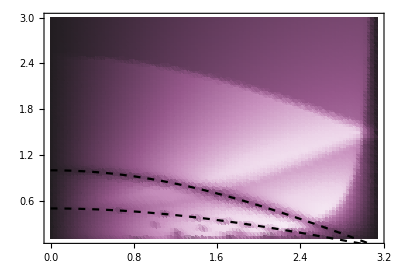

```mathematica
(*Final setup of the master equation and solution.*)
masterVec=Flatten@MapThread[Equal,{D[ρMat,t],ρDotMat},2];

ϕ0min=0/2;
ϕ0max=π;
ϕ0steps=96;
ϕ0stepsize=(ϕ0max-ϕ0min)/(ϕ0steps-1);

ωDmin=1/10;
ωDmax=3/1;
ωDsteps=64;
ωDstepsize=(ωDmax-ωDmin)/(ωDsteps-1);

unsortedCurrentMap=Reap[ParallelDo[
param={ϵ->1,δp->(1/100)*ϵ,δm->(1/1000)*ϵ,ϕ->ϕ0val+2sD*Cos[ωDval*t],ϕ0->ϕ0val,sw->-2sD*ωDval*Sin[ωDval*t],sD->(1/10)*(ϵ/((ℏ)*ωDval)),ωD->ωDval,Γ0->(*10^(-2)*)10^(-3)*ϵ,ΓD->(*10^(-3)*)10^(-5),Ec->100,Δ->(3/2)*(ϵ),ℏ->1,Γq->10^(-4)*(ϵ/(ℏ)),Γr->10^(-4)*(ϵ/(ℏ)),Γd->10^(-3)*(ϵ/(ℏ))};
period=(2π/ωDval);
exptTime=400period;

initialCond=(Flatten@(MapThread[Equal,{ρMat,SparseArray[{{1,1}->1/3,{2,2}->1/3,{3,3}->1/6,{4,4}->1/6},{4,4}]},2])//.param)/.t->0;
syst=Join[masterVec,initialCond];

soln=NDSolve[syst//.param,ρFlat//.param,{t,exptTime-period,exptTime},MaxSteps->∞,Method->{"EquationSimplification"->"Solve"}];

initialT=exptTime-period;
finalT=exptTime;
tempInt=Chop[(2/(finalT-initialT))NIntegrate[Tr[(ρMat.CurHam//.param)/.Flatten[soln]],{t,initialT,finalT},Method->{"GlobalAdaptive","SymbolicProcessing"->0,"MaxErrorIncreases"->2000},MaxRecursion->20,WorkingPrecision->120,PrecisionGoal->8,AccuracyGoal->Infinity],10^(-5)];
ParallelSow[{ϕ0val,ωDval,tempInt}];
Clear[tempInt];
Clear[soln];
,{ϕ0val,ϕ0min,ϕ0max,ϕ0stepsize},{ωDval,ωDmin,ωDmax,ωDstepsize},Method->"FinestGrained"]][[2,1]];//AbsoluteTiming

currentMap=Sort[unsortedCurrentMap,(#1[[1]]<#2[[1]]||(#1[[1]]==#2[[1]]&&#1[[2]]<#2[[2]]))&];
Clear[unsortedCurrentMap];

spike1=Plot[(ϵ[2]-ϵ[1])/.{ϵ->1,δm->1/1000},{ϕ,0,π},PlotStyle->{Black,Dashed}];
spike2=Plot[(1/2)(ϵ[2]-ϵ[1])/.{ϵ->1,δm->1/1000},{ϕ,0,π},PlotStyle->{Black,Dashed}];
Show[ListDensityPlot[currentMap,PlotLegends->Automatic,ColorFunction->ColorData["FuchsiaTones"],AspectRatio->2/3],spike1,spike2]
```